```mathematica
plotBuffer[path_,opts:OptionsPattern[]]:=Module[{file,headings,points},
file=Import[path];
headings=file//First;
points=file//Rest;
data=Most[points]//Transpose;
Print[Join[{headings},Take[points,-10]]//TableForm];
Print["Total # of particles: ",points⟦-2⟧//Total];
ListLinePlot[
data,
PlotLegends->headings,
AxesLabel->{"timestep","Number of particles"},
DataRange->{0,(Length[data//Transpose])*10},
GridLines->Automatic,
opts
]
]
```

```mathematica
plotBuffer["D:\\measureBuffer\\countCells.csv"]
```

nPellets | nBuffer | nEnergy | nCells
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22616 | 71804 | 5580 | 0

Total # of particles: 100000

-Graphics-

```mathematica
Export["D:\\measureBuffer 3\\bufferplot 3.png",%217,ImageResolution->300]
```

D:\measureBuffer 3\bufferplot 3.png

nDetritus | nBuffer | nEnergy | nCells
17288 | 15228 | 30000 | 47484
17277 | 15231 | 30000 | 47492
17270 | 15254 | 30000 | 47476
17264 | 15279 | 30000 | 47457
17257 | 15240 | 30000 | 47503
17247 | 15245 | 30000 | 47508
17246 | 15248 | 30000 | 47506
17242 | 15275 | 30000 | 47483
17242 | 15274 | 30000 | 47484
17227 | 15280 | 30000 | 47493

Total # of particles: 110000

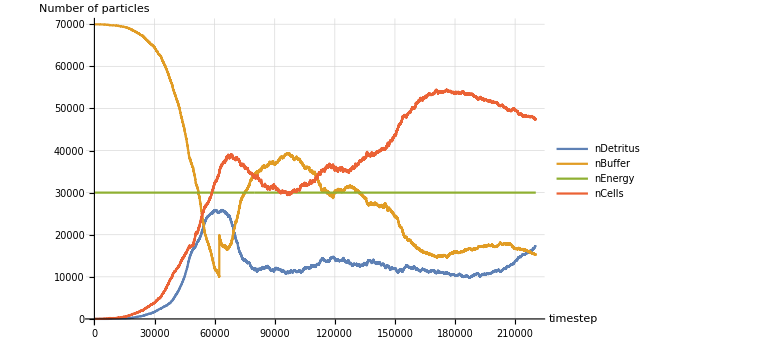

```mathematica
plotBuffer["D:\\measureBuffer 3\\countCells.csv",ImageSize->Large]
```

```mathematica
plotBuffer["D:\\workingBuffer\\countCells.csv",ImageSize->Large]
```

nDetritus | nBuffer | nEnergy | nCells
16320 | 73658 | 30000 | 22
16320 | 73658 | 30000 | 22
16319 | 73659 | 30000 | 22
16319 | 73659 | 30000 | 22
16318 | 73660 | 30000 | 22
16317 | 73661 | 30000 | 22
16317 | 73661 | 30000 | 22
16317 | 73661 | 30000 | 22
16317 | 73661 | 30000 | 22
16316 | 73662 | 30000 | 22

Total # of particles: 120000

-Graphics-

```mathematica
plotBuffer["D:\\newOutput\\countCells.csv",ImageSize->Large,PlotRange->Full]
```

nDetritus | nBuffer | nEnergy | nCells
57584 | 34627 | 30000 | 17843
57575 | 34642 | 30000 | 17837
57635 | 34572 | 30000 | 17847
57622 | 34557 | 30000 | 17875
57648 | 34517 | 30000 | 17889
57626 | 34540 | 30000 | 17888
57603 | 34566 | 30000 | 17885
57588 | 34526 | 30000 | 17940
57607 | 34509 | 30000 | 17938
57620 | 34530 | 3 |

Total # of particles: 140054

-Graphics-

```mathematica
plotBuffer["D:\\globalCoord\\countCells.csv",ImageSize->Large,PlotRange->Full]
```

nDetritus | nBuffer | nEnergy | nCells
132513 | 41093 | 30000 | 26448
132498 | 41063 | 30000 | 26493
132497 | 41068 | 30000 | 26489
132479 | 41091 | 30000 | 26484
132454 | 41122 | 30000 | 26478
132475 | 41081 | 30000 | 26498
132462 | 41114 | 30000 | 26478
132465 | 41111 | 30000 | 26478
132444 | 41139 | 30000 | 26471
132467 | 41174 | 30000 | 26413

Total # of particles: 230054

-Graphics-